```mathematica
M=30;
Mshort=10
M1=M;M2=M;M3=M;MaxIndex=Max[{M1,M2,M3}]
```

10

30

```mathematica
Coeff=Table[({{0}, {0}, {0}, {0}}),{i,0,M1},{j,0,M2},{k,0,M3}]; (*Coefficients for parameterization method *)
Coeff[[2,1,1]]=({{0}, {1}, {0}, {0}});Coeff[[1,2,1]]=({{0}, {0}, {1}, {0}});Coeff[[1,1,2]]=({{0}, {0}, {0}, {1}}); (* Define initial Eigenvectors*)
```

### Removing Resonances

Define function, and the parameterization as a series with coefficients

```mathematica
f[c0_,c1_,c2_,c3_]:=({{c0^2+2 c1^2+2 c2^2+2 c3^2}, {-c1+2 c0 c1+2 c1 c2+2c3 c2}, {-4c2 +2 c0 c2+c1^2+2c3 c1}, {-9 c3 +2 c0 c3+2  c1 c2}})
F[P_]:=f[P[[1]],P[[2]],P[[3]],P[[4]]]
P[θ1_,θ2_,θ3_]:=Sum[Coeff[[i+1,j+1,k+1]]If[i==0,1,θ1^i]If[j==0,1,θ2^j]If[k==0,1,θ3^k],{i,0,M1},{j,0,M2},{k,0,M3}]
```

```mathematica
XX=({{a}, {b}, {c}, {d}});(* dummy vector to solve for coefficients *)
```

```mathematica
Clear[β,δ,α,γ]
```

Define the conjugate system

```mathematica
α=1;
β=11/81;
γ=1;
δ=19/24;
h[θ1_,θ2_,θ3_]:=({{-θ1}, {-4 θ2+α/3 θ1^4}, {-9θ3+β θ1^9-γ θ1 θ2^2+δ θ1^5 θ2^1}})
```

Solve for the (p,q,r) coefficient

```mathematica
(*
For[coeffNorm=2,coeffNorm<=MaxIndex,coeffNorm++,Print[coeffNorm]
For[p=0,p<=coeffNorm,p++,
For[q=0,q<=coeffNorm-p,q++,
r=coeffNorm-p-q;
Print["(p,q,r)=(",p,",",q,",",r,")"];
]
]
]
```

```mathematica
timeStart=AbsoluteTime[];
For[coeffNorm=2,coeffNorm<=Mshort,coeffNorm++,Print[coeffNorm]
For[p=0,p<=coeffNorm,p++,
For[q=0,q<=coeffNorm-p,q++,
r=coeffNorm-p-q;
XX=({{a}, {b}, {c}, {d}});(* dummy vector to solve for coefficients *)
Coeff[[1+p,1+q,1+r]]=XX;
P[θ1_,θ2_,θ3_]=Sum[Coeff[[i+1,j+1,k+1]]If[i==0,1,θ1^i]If[j==0,1,θ2^j]If[k==0,1,θ3^k],{i,0,coeffNorm},{j,0,coeffNorm},{k,0,coeffNorm}];
JacP[θ1_,θ2_,θ3_]=Table[{
D[P[θ1,θ2,θ3],θ1][[i,1]],
D[P[θ1,θ2,θ3],θ2][[i,1]],
D[P[θ1,θ2,θ3],θ3][[i,1]]},{i,1,4}];

xx=Flatten[F[P[θ1,θ2,θ3]]- JacP[θ1,θ2,θ3].h[θ1,θ2,θ3]];
reduce=Normal[Series[xx,{θ1,0,p},{θ2,0,q},{θ3,0,r}]];
sol=Solve[1/(θ1^p θ2^q θ3^r)reduce=={0,0,0,0},{a,b,c,d}];
newCoeff=Evaluate[XX/.sol][[1]];
newCoeff=newCoeff/.{a->0,b->0,c->0,d->0};(*In case there is a free variable, we set it equal to zero *) 
Coeff[[1+p,1+q,1+r]]=newCoeff;
]
]
]
timeStop=AbsoluteTime[];
```

2

3

4

5

6

7

8

9

10

```mathematica
timeStop-timeStart
```

100.871123

```mathematica
Table[MatrixForm[Coeff[[1+i,1+j,1]]],{i,0,M},{j,0,0}]//N
Table[MatrixForm[Coeff[[1+i,1+j,1]]],{i,0,M},{j,1,1}];
Table[MatrixForm[Coeff[[1+i,1+j,1]]],{i,0,M},{j,2,2}];
Table[MatrixForm[Coeff[[1+i,1+j,1]]],{i,0,M},{j,3,3}];
```

{{(0.
0.
0.
0.)},{(0.
1.
0.
0.)},{(-1.
0.
0.5
0.)},{(0.
0.5
0.
0.166667)},{(-0.875
0.
0.
0.)},{(0.
0.479167
0.
0.)},{(-0.703704
0.
-0.0833333
0.)},{(0.
0.447917
0.
-0.114583)},{(-0.587312
0.
-0.11169
0.)},{(0.
0.415925
0.
0.)},{(-0.500151
0.
-0.166868
0.)}}

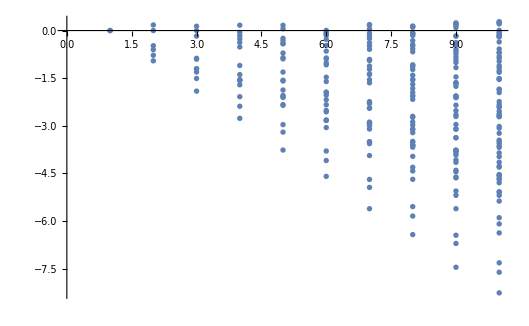

```mathematica
CoeffNorms=Flatten[Table[{i+j+k,Log[Norm[Coeff[[1+i,1+j,1+k]],1]]/Log[10]},{i,0,M1},{j,0,M2},{k,0,M3}],2];
ListPlot[CoeffNorms]
```

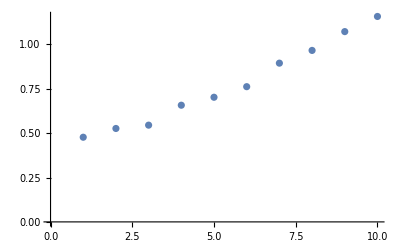

```mathematica
SingleCoeffNormList=Table[{indexNorm,1/Log[10] Log[Sum[Norm[Coeff[[1+p,1+q,1+(indexNorm-p-q)]],1],{p,0,indexNorm},{q,0,indexNorm-p}]]},{indexNorm,1,M}];
ListPlot[SingleCoeffNormList]
```

```mathematica
0.06717167290595542
```

0.0671717

```mathematica
lm=LinearModelFit[SingleCoeffNormList,x,x]
```

FittedModel[0.348745+0.0777183 x]

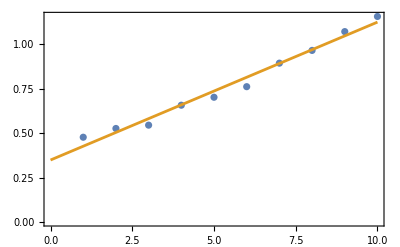

```mathematica
Show[ListPlot[SingleCoeffNormList],Plot[{,lm[x]},{x,0,M}],Frame->True]
```

```mathematica
slope=D[Normal[lm],x]
```

0.0777183

```mathematica
radiusOfConvergence=10^-slope
```

0.836145

```mathematica
radiusOfConvergence=.775;
```

```mathematica
𝒟=Disk[{0,0},radiusOfConvergence];
ParametricPlot3D[Flatten[({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}}).P[θ1,θ2,0]],{θ1,θ2}∈𝒟,Mesh->True]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Flatten[({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}).P[θ1,θ2,0]],{θ1,θ2}∈𝒟,Mesh->True]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Flatten[({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}).P[0,θ2,θ3]],{θ2,θ3}∈𝒟,Mesh->True]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Flatten[({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}).P[θ1,0,θ3]],{θ1,θ3}∈𝒟,Mesh->True]
```

-Graphics3D-

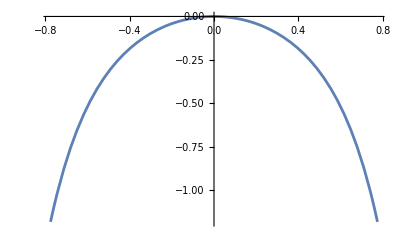

```mathematica
Plot[P[θ1,0,0][[1]],{θ1,-radiusOfConvergence,radiusOfConvergence}]
```

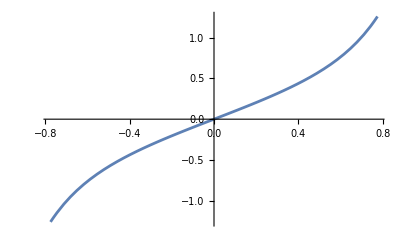

```mathematica
Plot[P[θ1,0,0][[2]],{θ1,-radiusOfConvergence,radiusOfConvergence}]
```

## Analytic Functions

```mathematica
DSolve[I{θ1'[t],θ2'[t],θ3'[t]}==Flatten[h[θ1[t],θ2[t],θ3[t]]],{θ1,θ2,θ3},t]//Simplify
```

{{θ1→Function[{t},ⅇ^(ⅈ t) C[1]],θ2→Function[{t},-1/3 ⅈ ⅇ^(4 ⅈ t) t C[1]^4+ⅇ^(4 ⅈ t) C[2]],θ3→Function[{t},-1/648 ⅈ ⅇ^(9 ⅈ t) (88 t C[1]^9-171/2 ⅈ t^2 C[1]^9+24 t^3 C[1]^9+513 t C[1]^5 C[2]+216 ⅈ t^2 C[1]^5 C[2]-648 t C[1] C[2]^2)+ⅇ^(9 ⅈ t) C[3]]}}

```mathematica
(-1/648 ⅈ ⅇ^(9 ⅈ t) (88 t C[1]^9-171/2 ⅈ t^2 C[1]^9+24 t^3 C[1]^9+513 t C[1]^5 C[2]+216 ⅈ t^2 C[1]^5 C[2]-648 t C[1] C[2]^2)+ⅇ^(9 ⅈ t) C[3])/ⅇ^(9 ⅈ t)//Expand
```

-11/81 ⅈ t C[1]^9-(19 t^2 C[1]^9)/144-1/27 ⅈ t^3 C[1]^9-19/24 ⅈ t C[1]^5 C[2]+1/3 t^2 C[1]^5 C[2]+ⅈ t C[1] C[2]^2+C[3]

```mathematica
Simplify[-19/24 ⅈ t C[1]^5 C[2]+1/3 t^2 C[1]^5 C[2]]
```

1/24 t (-19 ⅈ+8 t) C[1]^5 C[2]

```mathematica
Expand[1/24 t (-19 ⅈ+8 t) ]
```

-(19 ⅈ t)/24+t^2/3

```mathematica
TeXForm[-(19 ⅈ t)/24+t^2/3]
```

\frac{t^2}{3}-\frac{19 i t}{24}

```mathematica
Expand[-11/81 ⅈ t C[1]^9-(19 t^2 C[1]^9)/144-1/27 ⅈ t^3 C[1]^9]
```

-11/81 ⅈ t C[1]^9-(19 t^2 C[1]^9)/144-1/27 ⅈ t^3 C[1]^9

```mathematica
Expand[(-11/81 ⅈ t C[1]^9-(19 t^2 C[1]^9)/144-1/27 ⅈ t^3 C[1]^9)/C[1]^9]
```

-(11 ⅈ t)/81-(19 t^2)/144-(ⅈ t^3)/27

```mathematica
TeXForm[-(-(11 ⅈ t)/81-(19 t^2)/144-(ⅈ t^3)/27)]
```

\frac{i t^3}{27}+\frac{19 t^2}{144}+\frac{11 i t}{81}

## Plot a point

```mathematica
radiusOfConvergence
```

0.775

```mathematica
P[radiusOfConvergence ,-.1,-.015]
```

{{-1.27328},{1.44128},{-0.00642404},{-0.0109567}}

```mathematica
{{-0.17260396247823911},{0.42144877280752335},{0.07472647855008092},{0.009547268849998215}}
```

```mathematica
{{-0.4747181609604299},{0.724418799379576},{0.16352244461924248},{0.030160972765692174}}
```

```mathematica
Manipulate[P[ρ radiusOfConvergence Sin[ϕ1]Cos[ϕ2],ρ radiusOfConvergence Sin[ϕ1]Sin[ϕ2],ρ radiusOfConvergence Cos[ϕ1]],{{ρ,1/2},0,1},{{ϕ1,π/2},0,π},{ϕ2,-π/2,π/2}]
```

## Set Initial Condition

```mathematica
Coeff
```

```mathematica
M
```

14

```mathematica
M=13
```

13

```mathematica
({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}).P[radiusOfConvergence,-.1,.00]
```

{{1.44377},{-0.023079},{0.0358602}}

```mathematica
M=14
```

14

```mathematica
?
```

```mathematica
?NSolve
```

```mathematica
?Root
```

```mathematica
a=0;b=0;c=0;d=0;
levelValue=.5
solStartingPoint=FindRoot[({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}).P[θ1,θ2,θ3]=={{levelValue},{0},{0}},{θ1,levelValue.9},{θ2,-.1},{θ3,0}]
Clear[a,b,c,d]
```

0.5

{θ1→0.430747,θ2→-0.074693,θ3→0.0056434}

```mathematica
P[θ1,θ2,θ3]/.solStartingPoint
```

```mathematica
{{-0.2234304501656292+2.644085833629319*^-37 a},{0.49999999999999994+2.644085833629319*^-37 b}, {0.+2.644085833629319*^-37 c},{-1.734723475976807*^-18+2.644085833629319*^-37 d}}
```

```mathematica
{{-0.22301402589701574},{0.5},{3.247780871122343*^-18},{2.0822404117323587*^-18}}
```

```mathematica
{{-0.4539934766090501},{0.7500000000000001},{3.2506889169066754*^-18},{5.121387996231098*^-18}}
```

```mathematica
{{-0.22301402589701574},{0.5},{3.247780871122343*^-18},{2.0822404117323587*^-18}}
```

```mathematica
M
```

17

```mathematica
coeffNorm-p
```

```mathematica
.5
```

```mathematica
(.43)^27
```

1.26955×10^-10

## Extended

```mathematica
timeStart=AbsoluteTime[];
For[coeffNorm=Mshort+1,coeffNorm<=M,coeffNorm++,Print[coeffNorm];
For[p=0,p<=coeffNorm,p++,
q=coeffNorm-p;
r=0;
XX=({{a}, {b}, {c}, {d}});(* dummy vector to solve for coefficients *)
Coeff[[1+p,1+q,1+r]]=XX;
P[θ1_,θ2_,θ3_]:=Sum[Coeff[[i+1,j+1,k+1]]If[i==0,1,θ1^i]If[j==0,1,θ2^j]If[k==0,1,θ3^k],{i,0,coeffNorm},{j,0,Mshort},{k,0,Mshort}];
JacP[θ1_,θ2_,θ3_]=Table[{
D[P[θ1,θ2,θ3],θ1][[i,1]],
D[P[θ1,θ2,θ3],θ2][[i,1]],
D[P[θ1,θ2,θ3],θ3][[i,1]]},{i,1,4}];

xx=Flatten[F[P[θ1,θ2,θ3]]- JacP[θ1,θ2,θ3].h[θ1,θ2,θ3]];
reduce=Normal[Series[xx,{θ1,0,p},{θ2,0,q},{θ3,0,r}]];
sol=Solve[1/(θ1^p θ2^q θ3^r)reduce=={0,0,0,0},{a,b,c,d}];
newCoeff=Evaluate[XX/.sol][[1]];
newCoeff=newCoeff/.{a->0,b->0,c->0,d->0};(*In case there is a free variable, we set it equal to zero *) 
Coeff[[1+p,1+q,1+r]]=newCoeff;
]
]
timeStop=AbsoluteTime[];
```

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

```mathematica
(.45)^20
```

1.15945×10^-7

```mathematica
Coeff[[99,1,1]]//N
```

{{-0.465925},{0.},{-0.370002},{0.}}

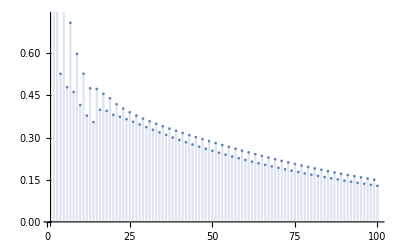

```mathematica
DiscretePlot[Norm[Coeff[[i,1,1]]],{i,1,M}]
```

```mathematica
P[θ1_,θ2_,θ3_]:=Sum[Coeff[[i+1,j+1,k+1]]If[i==0,1,θ1^i]If[j==0,1,θ2^j]If[k==0,1,θ3^k],{i,0,M},{j,0,Mshort},{k,0,Mshort}];
```

```mathematica
a=0;b=0;c=0;d=0;
levelValue=.5
solStartingPoint=FindRoot[({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}).P[θ1,θ2,θ3]=={{levelValue},{0},{0}},{θ1,levelValue.9},{θ2,-.1},{θ3,0}]
Clear[a,b,c,d]
P[θ1,θ2,θ3]/.solStartingPoint
```

0.5

{θ1→0.430066,θ2→-0.0739878,θ3→0.00530985}

```mathematica
{{-0.22301410031755192},{0.5},{-1.0408340855860843*^-17},{4.336808689942018*^-18}}
```

```mathematica
{{-0.2230033084554396},{0.5000000000000001},{-2.2131965060130003*^-17},{2.703671264992848*^-18}}
```